## Initial analysis of Fibonacci points (old scratch work)

```mathematica
P={1,1,.853553,.710042,.516735, .334845, .235879,.168727, .12875,.0923583,.0619449,.0436916};
```

```mathematica
(*Data added from Alden's program*)
P1={0.092358,0.061945,0.043692,0.033011,0.024439,0.017544,0.01199,0.008791,0.006149,0.004568,0.003277,0.002367};


P2 = {1,1,.853553,.710042,.516735, .334845, .235879,.168727, .12875,.0923583,.0619449,.0436916,0.033011,0.024439,0.017544,0.01199,0.008791,0.006149,0.004568,0.003277,0.002367}//Chop
```

{1,1,0.853553,0.710042,0.516735,0.334845,0.235879,0.168727,0.12875,0.0923583,0.0619449,0.0436916,0.033011,0.024439,0.017544,0.01199,0.008791,0.006149,0.004568,0.003277,0.002367}

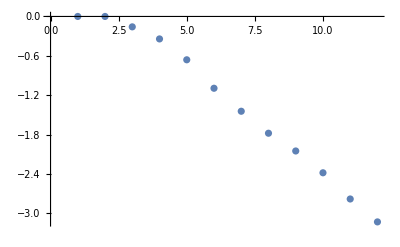

```mathematica
ListPlot[Log[#]&@P]
```

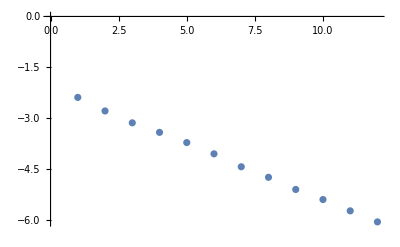

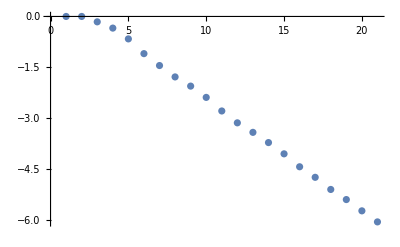

```mathematica
ListPlot[Log[#]&@P1]
ListPlot[Log[#]&@P2]
```

{-2.38208,-2.78151,-3.13059,-3.41091,-3.71158,-4.04304,-4.42368,-4.73403,-5.09147,-5.38868,-5.72083,-6.04613}

{{Log[89],-2.38208},{Log[144],-2.78151},{Log[233],-3.13059},{Log[377],-3.41091},{Log[610],-3.71158},{Log[987],-4.04304},{Log[1597],-4.42368},{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}

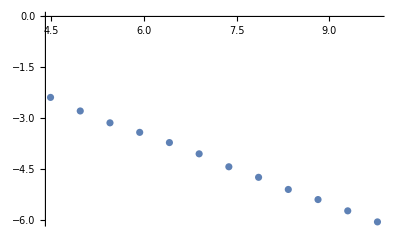

({{Log[89],-2.38208},{Log[144],-2.78151},{Log[233],-3.13059},{Log[377],-3.41091},{Log[610],-3.71158},{Log[987],-4.04304},{Log[1597],-4.42368},{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[144],-2.78151},{Log[233],-3.13059},{Log[377],-3.41091},{Log[610],-3.71158},{Log[987],-4.04304},{Log[1597],-4.42368},{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[233],-3.13059},{Log[377],-3.41091},{Log[610],-3.71158},{Log[987],-4.04304},{Log[1597],-4.42368},{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[377],-3.41091},{Log[610],-3.71158},{Log[987],-4.04304},{Log[1597],-4.42368},{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[610],-3.71158},{Log[987],-4.04304},{Log[1597],-4.42368},{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[987],-4.04304},{Log[1597],-4.42368},{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[1597],-4.42368},{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[2584],-4.73403},{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[4181],-5.09147},{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[6765],-5.38868},{Log[10946],-5.72083},{Log[17711],-6.04613}}
{{Log[10946],-5.72083},{Log[17711],-6.04613}})

(0.656302-0.68603 x
0.61834-0.681388 x
0.63391-0.683255 x
0.692856-0.690191 x
0.710957-0.692281 x
0.665437-0.68712 x
0.557258-0.675073 x
0.56683-0.67612 x
0.455838-0.664187 x
0.634981-0.683121 x
0.566579-0.676012 x)

```mathematica
Q1=Log[#]&@P1
RR1={Table[Log[Fibonacci[i+10]],{i,Length[Q1]}],Q1}//Transpose
ListPlot[Drop[RR1,0]]
DrRR1[t_]:=Drop[RR1,t-1]
Table[DrRR1[i],{i,Length[Q1]-1}]//MatrixForm
Table[Fit[DrRR1[i],{1,x},x],{i,Length[Q1]-1}]//MatrixForm
```

```mathematica
Q=Log[#]&@P;
RR={Table[Log[Fibonacci[i]],{i,Length[Q]}],Q}//Transpose
```

{{0,0},{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}

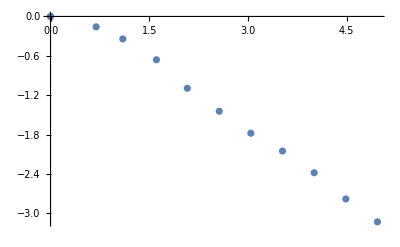

({{0,0},{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[89],-2.78151},{Log[144],-3.1306}})

(0.194354-0.646505 x
0.260558-0.665517 x
0.395164-0.704171 x
0.43595-0.715185 x
0.429603-0.713532 x
0.360279-0.696243 x
0.371684-0.69898 x
0.434408-0.713471 x
0.62901-0.756827 x
0.726055-0.777701 x
0.474954-0.725491 x)

```mathematica
ListPlot[Drop[RR,0]]
DrRR[t_]:=Drop[RR,t-1]
Table[DrRR[i],{i,Length[Q]-1}]//MatrixForm
Table[Fit[DrRR[i],{1,x},x],{i,Length[Q]-1}]//MatrixForm
```

{0,0,-0.158348,-0.342431,-0.660225,-1.09409,-1.44444,-1.77947,-2.04988,-2.38208,-2.78151,-3.1306,-3.41091,-3.71158,-4.04304,-4.42368,-4.73403,-5.09147,-5.38868,-5.72083,-6.04613}

{{0,0},{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}

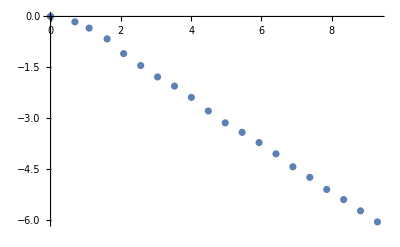

({{0,0},{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[89],-2.78151},{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[144],-3.1306},{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[233],-3.41091},{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[377],-3.71158},{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[610],-4.04304},{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[987],-4.42368},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[2584],-5.09147},{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[4181],-5.38868},{Log[6765],-5.72083},{Log[10946],-6.04613}}
{{Log[6765],-5.72083},{Log[10946],-6.04613}})

(0.245978-0.672829 x
0.29365-0.680318 x
0.364242-0.691408 x
0.375729-0.693151 x
0.362287-0.691153 x
0.330162-0.686495 x
0.328788-0.6863 x
0.335161-0.687184 x
0.348421-0.688981 x
0.326145-0.686026 x
0.290455-0.681389 x
0.305105-0.683253 x
0.360731-0.690191 x
0.377821-0.692281 x
0.334788-0.68712 x
0.232404-0.675073 x
0.241473-0.67612 x
0.136224-0.664187 x
0.306255-0.683121 x
0.241274-0.676012 x)

```mathematica
Q2=Log[#]&@P2
RR2={Table[Log[Fibonacci[i]],{i,Length[Q2]}],Q2}//Transpose
ListPlot[Drop[RR2,0]]
DrRR2[t_]:=Drop[RR2,t-1]
Table[DrRR2[i],{i,Length[Q2]-1}]//MatrixForm
Table[Fit[DrRR2[i],{1,x},x],{i,Length[Q2]-1}]//MatrixForm
```

```mathematica
Table[{Fibonacci[i],{1,1,0.853553,0.710042,0.516735,0.334845,0.235879,0.168727,0.12875,0.0923583,0.0619449,0.0436916,0.033011,0.024439,0.017544,0.01199,0.008791,0.006149,0.004568,0.003277,0.002367}[[i]]},{i,1,21}]
```

{{1,1},{1,1},{2,0.853553},{3,0.710042},{5,0.516735},{8,0.334845},{13,0.235879},{21,0.168727},{34,0.12875},{55,0.0923583},{89,0.0619449},{144,0.0436916},{233,0.033011},{377,0.024439},{610,0.017544},{987,0.01199},{1597,0.008791},{2584,0.006149},{4181,0.004568},{6765,0.003277},{10946,0.002367}}

## Analysis of Spiral points

### Fibonacci Points

```mathematica
P31={

{1,1},

{3,0.710042},

{8,0.334845},

{21,0.168727},

{55,0.0923583},

{144,0.0436916},

{377,0.024439},

{987,0.01199},

{2584,0.006149},

{6765,0.003277}

};
P32={
{1,1},

{2,0.853553},

{5,0.516735},

{13,0.235879},

{34,0.12875},

{89,0.0619449},

{233,0.033011},

{610,0.017544},

{1597,0.008791},

{4181,0.004568},

{10946,0.002367}
};

P3={
{1,1},
{2,0.853553},
{3,0.710042},
{5,0.516735},
{8,0.334845},
{13,0.235879},
{21,0.168727},
{34,0.12875},
{55,0.0923583},
{89,0.0619449},
{100,.062205},
{144,0.0436916},
{200,0.034656},
{233,0.033011},
{300,0.028740},
{377,0.024439},
{400,0.021869},
{500,0.019336},
{600,0.017426},
{610,0.017544},
{700,0.017065},
{800,0.014727},
{900,0.013625},
{987,0.01199},
{1000,0.011877},
{1100,0.011451},
{1200,0.011292},
{1300,0.010228},
{1400,0.009928},
{1500, 0.009174},
{1597,0.008791},
{2584,0.006149},
{3000,0.005789},
{4181,0.004568},
{6765,0.003277},
{10946,0.002367}
};
```

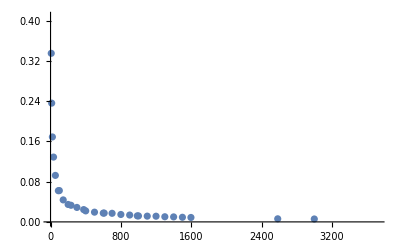

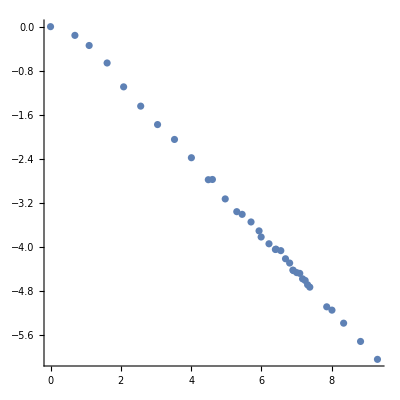

(0.294093-0.679361 x
0.360592-0.689556 x
0.370702-0.691079 x
0.357602-0.689125 x
0.328325-0.684812 x
0.327736-0.684726 x
0.334251-0.685664 x
0.346217-0.687368 x
0.332385-0.685423 x
0.315481-0.683077 x
0.331731-0.685298 x
0.302853-0.681367 x
0.332744-0.685386 x
0.373236-0.690759 x
0.386361-0.69249 x
0.376485-0.691203 x
0.36782-0.690088 x
0.412359-0.6958 x
0.438905-0.699157 x
0.451335-0.700708 x
0.451703-0.700754 x
0.389089-0.693034 x
0.365141-0.690115 x
0.332726-0.686209 x
0.35871-0.689309 x
0.396153-0.693771 x
0.406195-0.694957 x
0.347171-0.688044 x
0.340442-0.687262 x
0.27779-0.680022 x
0.26384-0.678418 x
0.223261-0.673768 x
0.370824-0.690288 x
0.306255-0.683121 x
0.241274-0.676012 x)

```mathematica
ListPlot[P3]
ListPlot[Log[#]&@P3,PlotRange->{0,-10},AspectRatio->1]
Table[Fit[Log[#]&@Drop[P3,i],{1,x},x],{i,0,Length[P3]-2}]//MatrixForm
```

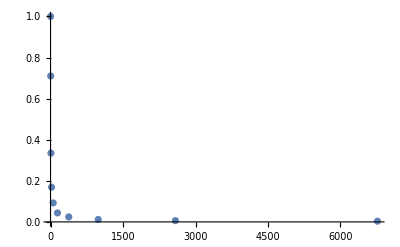

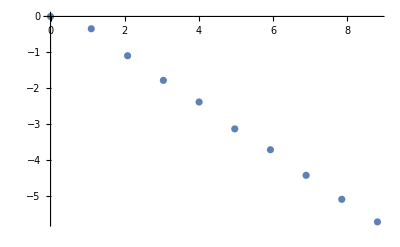

(0.238468-0.672455 x
0.370474-0.693696 x
0.334344-0.688196 x
0.331649-0.687805 x
0.357267-0.691356 x
0.2841-0.681647 x
0.394479-0.695695 x
0.216196-0.673895 x
0.0465512-0.653934 x)

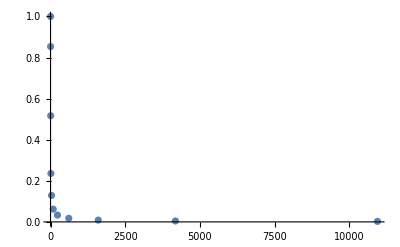

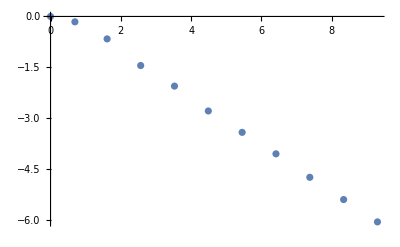

(0.252768-0.673158 x
0.360523-0.689733 x
0.38412-0.693229 x
0.328143-0.685297 x
0.344373-0.687498 x
0.296217-0.681241 x
0.345911-0.687439 x
0.387362-0.69241 x
0.294336-0.681667 x
0.307395-0.683121 x)

```mathematica
ListPlot[P31]
ListPlot[Log[#]&@P31]
Table[Fit[Log[#]&@Drop[P31,i],{1,x},x],{i,0,Length[P31]-2}]//MatrixForm
ListPlot[P32]
ListPlot[Log[#]&@P32]
Table[Fit[Log[#]&@Drop[P32,i],{1,x},x],{i,0,Length[P32]-2}]//MatrixForm
```

### Sqrt[2] spiral points

```mathematica
P4={
{100,0.065078},
{200,0.043376},
 {300,0.030375},
{400,0.026812},
{500, 0.021833}, 
{600,0.020017}, 
{700,0.017800},
 {800,0.016016},
 {900, 0.015092},
 {1000, 0.013333}, 
{1100, 0.012613},
 {1200, 0.012104},
{1300,0.011831},
{1400,0.011573},
{1500,0.010722},
{3000,0.006545}
};
```

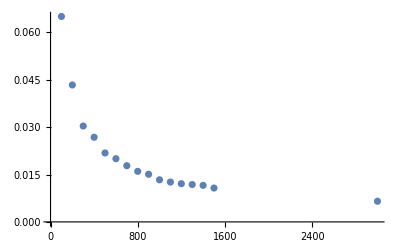

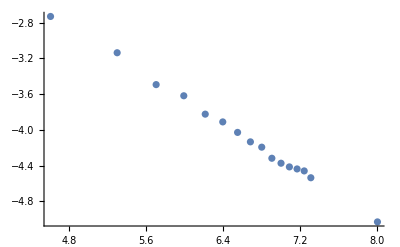

(0.413041-0.67867 x
0.455636-0.684838 x
0.376394-0.673538 x
0.447862-0.68361 x
0.36828-0.672506 x
0.408312-0.678041 x
0.348945-0.669905 x
0.30875-0.664445 x
0.314089-0.665164 x
0.241728-0.655516 x
0.38531-0.674463 x
0.564447-0.697835 x
0.748683-0.721578 x
0.841202-0.733351 x
0.672352-0.712109 x)

```mathematica
ListPlot[P4]
ListPlot[Log[#]&@P4]
Table[Fit[Log[#]&@Drop[P4,i],{1,x},x],{i,0,Length[P4]-2}]//MatrixForm
```

### Sqrt[3] spiral points

```mathematica
P5={
{100, 0.061732},
{200,0.042712},
{300, 0.030685},
{400, 0.024324},
{500,0.020715},
{600, 0.017470},
{700, 0.015525},
{800, 0.015064},
{900, 0.013914},
{1000, 0.013516},
{1100,0.012222}, 
{1200,0.011957},
{1300,0.011158},
{1400,0.011342},
{1500,0.009936},
{3000,0.006612}
};
```

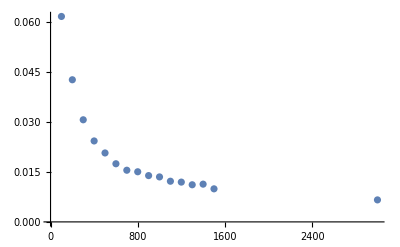

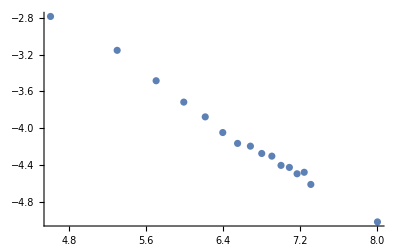

(0.316396-0.671543 x
0.33526-0.674275 x
0.145118-0.647161 x
-0.00905128-0.625432 x
-0.118625-0.610143 x
-0.219916-0.596139 x
-0.173812-0.602457 x
-0.0117854-0.624466 x
0.024933-0.629409 x
0.102711-0.63978 x
0.0433858-0.631951 x
0.157464-0.646835 x
0.144329-0.645142 x
0.254451-0.659155 x
-0.3145-0.587578 x)

```mathematica
ListPlot[P5]
ListPlot[Log[#]&@P5]
Table[Fit[Log[#]&@Drop[P5,i],{1,x},x],{i,0,Length[P5]-2}]//MatrixForm
```

### E spiral points (E has unbounded partial fraction terms, implies well approx)

```mathematica
P6={
{100, 0.064427},
{200, .037159},
{300, .029520},
{400, .025569},
{500, .023318},
{600,0.021306},
{700, 0.019770},
{800,0.017100},
{900,0.015229},
{1000,0.014380},
{1100,0.014248},
{1200,0.013635},
{1300, 0.012507},
{1400,0.011701},
{1500,0.011318}
};
```

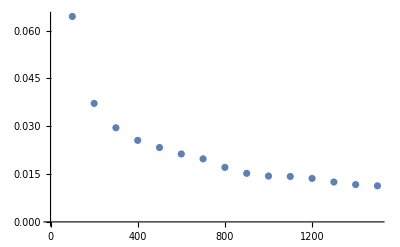

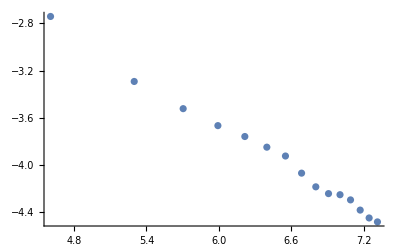

(0.0475677-0.616854 x
-0.094016-0.595947 x
0.0358317-0.614862 x
0.231507-0.643086 x
0.441581-0.673148 x
0.540441-0.687199 x
0.489081-0.679942 x
0.0690777-0.620913 x
-0.108196-0.596118 x
0.317054-0.655334 x
1.30401-0.792201 x
1.68908-0.845396 x
0.636744-0.700545 x
-0.9537-0.482368 x)

```mathematica
ListPlot[P6]
ListPlot[Log[#]&@P6]
Table[Fit[Log[#]&@Drop[P6,i],{1,x},x],{i,0,Length[P6]-2}]//MatrixForm
```

## Re above with sphCFLPSd: correct denominator points

### E spiral points (E has unbounded partial fraction terms, implies well approx)

```mathematica
P7=
{
{32,0.130697,{-0.807084,0.507061,0.302498}},
{39,0.114244,{-0.722431,0.657787,0.213098}},
{71,0.074633,{.600614,-0.614480,0.511544}},
{465,0.023885,{-0.275458,0.493863,0.824756}},
{536,0.021807,{-0.338102,-0.510492,0.790623}},
{1001,0.014109,{0.727411,0.370425,0.577632}}


}
```

{{32,0.130697,{-0.807084,0.507061,0.302498}},{39,0.114244,{-0.722431,0.657787,0.213098}},{71,0.074633,{0.600614,-0.61448,0.511544}},{465,0.023885,{-0.275458,0.493863,0.824756}},{536,0.021807,{-0.338102,-0.510492,0.790623}},{1001,0.014109,{0.727411,0.370425,0.577632}}}

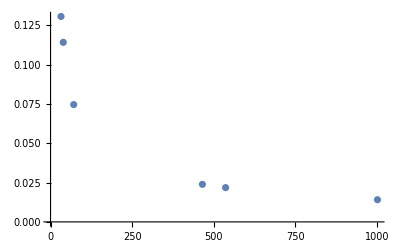

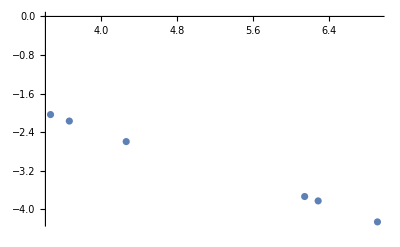

(0.15438-0.636143 x
0.130116-0.63226 x
0.0692048-0.622646 x
0.50527-0.689777 x
0.555096-0.697092 x)

```mathematica
ListPlot[Part[#,{1,2}]&/@P7]
ListPlot[Log[#]&@(Part[#,{1,2}]&/@P7)]
Table[Fit[Log[#]&@Drop[(Part[#,{1,2}]&/@P7),i],{1,x},x],{i,0,Length[P7]-2}]//MatrixForm
```

```mathematica
ListPlot[{Drop[Drop[RR,0],-2],Drop[Log[{Table[i,{i,60}],ZZ}]//Transpose,1]},PlotLegends->{"Spiral Points","Uniform Points"}]//Export["loglog.pdf",#]&
```

loglog.pdf